```mathematica
矩形孔的衍射
```

{2012,2,10,11,15,24.6640625}

{2012,2,10,11,15,24.7978515}

{2012,2,10,11,15,24.9277343}

{2012,2,10,11,15,25.0576171}

{2012,2,10,11,15,25.1884765}

{2012,2,10,11,15,25.321289}

{2012,2,10,11,15,25.453125}

{2012,2,10,11,15,25.5839843}

{2012,2,10,11,15,25.7177734}

{2012,2,10,11,15,25.8496093}

{2012,2,10,11,15,25.9814453}

{2012,2,10,11,15,26.1123046}

{2012,2,10,11,15,26.2441406}

{2012,2,10,11,15,26.3769531}

{2012,2,10,11,15,26.508789}

{2012,2,10,11,15,26.6376953}

{2012,2,10,11,15,26.7675781}

{2012,2,10,11,15,26.8974609}

{2012,2,10,11,15,27.0273437}

{2012,2,10,11,15,27.1591796}

{2012,2,10,11,15,27.2890625}

{2012,2,10,11,15,27.4189453}

{2012,2,10,11,15,27.5488281}

{2012,2,10,11,15,27.6777343}

{2012,2,10,11,15,27.8085937}

{2012,2,10,11,15,27.9384765}

{2012,2,10,11,15,28.0683593}

{2012,2,10,11,15,28.1992187}

{2012,2,10,11,15,28.3300781}

{2012,2,10,11,15,28.461914}

{2012,2,10,11,15,28.5917968}

{2012,2,10,11,15,28.7226562}

{2012,2,10,11,15,28.8535156}

{2012,2,10,11,15,28.984375}

{2012,2,10,11,15,29.1152343}

{2012,2,10,11,15,29.2460937}

{2012,2,10,11,15,29.3789062}

{2012,2,10,11,15,29.5126953}

{2012,2,10,11,15,29.6435546}

{2012,2,10,11,15,29.7763671}

{2012,2,10,11,15,29.9082031}

{2012,2,10,11,15,30.040039}

{2012,2,10,11,15,30.171875}

{2012,2,10,11,15,30.3037109}

{2012,2,10,11,15,30.4384765}

{2012,2,10,11,15,30.571289}

{2012,2,10,11,15,30.703125}

{2012,2,10,11,15,30.8359375}

{2012,2,10,11,15,30.9726562}

{2012,2,10,11,15,31.1083984}

{2012,2,10,11,15,31.2402343}

{2012,2,10,11,15,31.3730468}

{2012,2,10,11,15,31.5058593}

{2012,2,10,11,15,31.6386718}

{2012,2,10,11,15,31.7802734}

{2012,2,10,11,15,31.9130859}

{2012,2,10,11,15,32.046875}

{2012,2,10,11,15,32.1816406}

{2012,2,10,11,15,32.3173828}

{2012,2,10,11,15,32.4521484}

{2012,2,10,11,15,32.5859375}

{2012,2,10,11,15,32.7265625}

{2012,2,10,11,15,32.8613281}

{2012,2,10,11,15,33.}

{2012,2,10,11,15,33.1347656}

{2012,2,10,11,15,33.2695312}

{2012,2,10,11,15,33.4042968}

{2012,2,10,11,15,33.5390625}

{2012,2,10,11,15,33.6748046}

{2012,2,10,11,15,33.8105468}

{2012,2,10,11,15,33.9453125}

{2012,2,10,11,15,34.0810546}

{2012,2,10,11,15,34.2197265}

{2012,2,10,11,15,34.359375}

{2012,2,10,11,15,34.4960937}

{2012,2,10,11,15,34.6318359}

{2012,2,10,11,15,34.7685546}

{2012,2,10,11,15,34.9052734}

{2012,2,10,11,15,35.0419921}

{2012,2,10,11,15,35.1787109}

{2012,2,10,11,15,35.3164062}

{2012,2,10,11,15,35.453125}

{2012,2,10,11,15,35.5908203}

{2012,2,10,11,15,35.7304687}

{2012,2,10,11,15,35.8701171}

{2012,2,10,11,15,36.008789}

{2012,2,10,11,15,36.1464843}

{2012,2,10,11,15,36.2841796}

{2012,2,10,11,15,36.421875}

{2012,2,10,11,15,36.5605468}

{2012,2,10,11,15,36.6992187}

{2012,2,10,11,15,36.836914}

{2012,2,10,11,15,36.9794921}

{2012,2,10,11,15,37.1191406}

{2012,2,10,11,15,37.258789}

{2012,2,10,11,15,37.3964843}

{2012,2,10,11,15,37.5371093}

{2012,2,10,11,15,37.6748046}

{2012,2,10,11,15,37.8154296}

{2012,2,10,11,15,37.9550781}

{2012,2,10,11,15,38.09375}

e:/data/cfx.dat

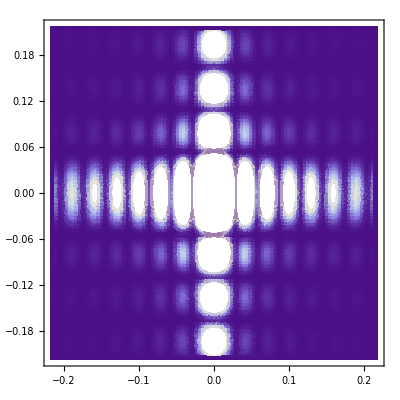

```mathematica
λ=0.6;q=2 π/λ;α0=β0=π/15.0;
r1=20.;r2=10.0;
n1=20;n2=50;intensity={};
δx=δy=r1/n1;
Do[
Do[
q1=q Sin[α];q2=q Sin[β];
u1=Sum[Cos[q1 x+q2 y],{x,-r1/2,r1/2,δx},
{y,-r2/2,r2/2,δy}];
u2=Sum[Sin[q1 x+q2 y],{x,-r1/2,r1/2,δx},
{y,-r2/2,r2/2,δy}];
AppendTo[intensity,
{Sin[α]/(√(1-Sin[α]^2-Sin[β]^2)),
Sin[β]/(√(1-Sin[α]^2-Sin[β]^2)),u1^2+u2^2}],
{α,-α0,α0,α0/n2}];Print[Date[]],
{β,-β0,β0,β0/n2}]
Export["e:/data/cfx.dat",intensity]
ListDensityPlot[intensity,Mesh->False]
Clear[α0,β0,u1,u2,intensity]
```